```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
Subscript[V, 0]=10.;a=0.5;L=1.;
n=11;
ϕ[k_?NumericQ]:=If[OddQ[k],Cos[(k π x)/(2L)],Sin[(k π x)/(2L)]]
```

```mathematica
H=Quiet@ParallelTable[If[Subscript[k, 1]==Subscript[k, 2],(Subscript[k, 1]^2 π^2)/8,0]+Subscript[V, 0] Quiet@NIntegrate[ϕ[Subscript[k, 1]]ϕ[Subscript[k, 2]],{x,-a,a},AccuracyGoal->4],{Subscript[k, 1],1,n},{Subscript[k, 2],1,n}];
```

```mathematica
H//MatrixForm;
{λ,ψ}=Eigensystem[H];
Reverse@Take[λ,-4]
```

{7.76594,8.75999,16.1812,25.6011}

```mathematica
ξ=NonlinearModelFit[Reverse@λ,k x^b,{k,b},x];
ξ["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 1.91432 | 0.18677 | 10.2496 | 2.91328×10^-6
b | 1.82647 | 0.0436527 | 41.8411 | 1.26863×10^-11

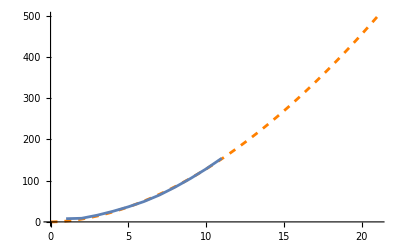

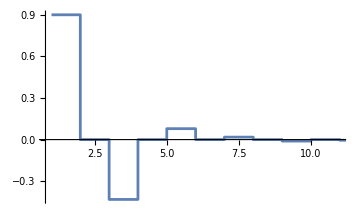

```mathematica
Show[Plot[ξ["BestFit"],{x,0,n+10},PlotStyle->{Dashed,Orange}],ListLinePlot[Reverse@λ,ImageSize->Medium]]
ListStepPlot[Last@ψ,PlotRange->Full,ImageSize->Medium]
```

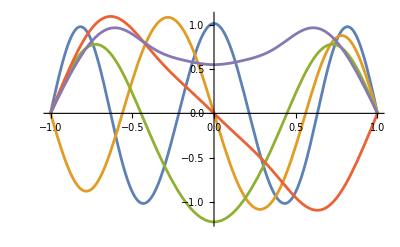

```mathematica
Ψ=#.Table[ϕ[k],{k,1,n}]&/@ψ;
With[{ξ=Take[Ψ,-5]},Plot[ξ,{x,-L,L}]]
```